#### Idea is to extend polymer artificially, fit spline, offset, find equidistant interpolation points on spline

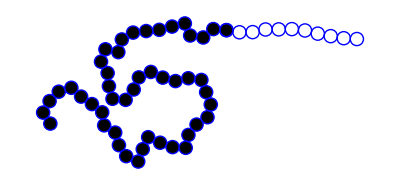

```mathematica
Graphics[{
Disk[#,1/2]&/@example["all particles"],Blue,Circle[#,1/2]&/@pts}]
```

```mathematica
interpolation = Interpolation[MapIndexed[{#2[[1]]-1,#}&,pts]]
```

InterpolatingFunction[…]

```mathematica
distSq[a_?NumericQ, b_?NumericQ,int_]:= (int[a]- int[b]).(int[a]- int[b])
```

```mathematica
build[ptList_,distSq_, int_]:=
Block[{lastPoint = ptList[[-1]],nextPoint},
nextPoint= t/.FindRoot[distSq[lastPoint,t,int]==1,{t,lastPoint+1,lastPoint,int[[1,1,2]]}];
Append[ptList,nextPoint]
]
```

```mathematica
ptList ={ RandomReal[{0,0.25}]}
```

{0.0926823}

```mathematica
While[Length[currentPoint]<= 47,
currentPoint=build[currentPoint,distSq,interpolation]
]
```

```mathematica
currentPoint
```

{0.2,1.32891,2.28877,3.27609,4.39344,5.36558,6.34998,7.41669,8.51691,9.58245,10.569,11.5174,12.8505,13.7698,14.9397,15.9296,16.9087,17.9613,18.9615,19.9584,20.9658,21.9676,22.96,23.9755,24.9725,25.9754,26.9717,27.9784,28.98,29.9769,30.9801,31.987,32.985,33.9845,34.9855,35.9905,36.9981,37.9985,38.9985,39.9984,40.9984,41.9978,42.999,43.9994,44.9994,45.9995,46.9995,47.9997}

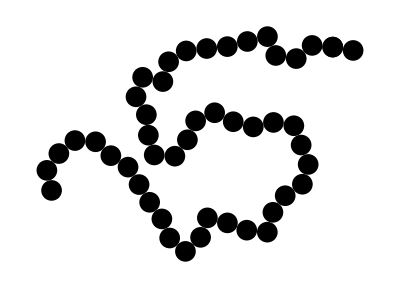

```mathematica
Graphics[{
Disk[#,1/2]&/@(interpolation/@currentPoint)}]
```

```mathematica
reptateWorm[positions_, dx_, dα_]:= 
Block[{interpolation, distSq, interpolationPoints = {dx},
extendPositions,reverse= RandomChoice[{Reverse,Identity}]},
distSq[a_?NumericQ, b_?NumericQ,int_]:= (int[a]- int[b]).(int[a]- int[b]);
lastAngle = ArcTan@@(positions[[-1]]-positions[[-2]]);
extendPositions = reverse@Join[positions,(Last[positions]+ #)&/@AnglePath[RandomReal[{-dα,dα},10]]];
interpolation=Interpolation[MapIndexed[{#2[[1]]-1,#}&,extendPositions]];
While[Length[interpolationPoints]<= Length[positions],
interpolationPoints=build[interpolationPoints,distSq,interpolation]
];
reverse[interpolation/@interpolationPoints]
]
```

```mathematica
(*example["all particles"]*)
```

{{-16.0081,-3.52977},{-16.5548,-2.69246},{-16.0649,-1.8207},{-15.3683,-1.10326},{-14.413,-0.807544},{-13.6713,-1.47828},{-12.8483,-2.04631},{-12.0715,-2.67601},{-11.9209,-3.66461},{-11.0845,-4.21283},{-10.801,-5.17178},{-10.2509,-6.00689},{-9.33789,-6.41485},{-8.99213,-5.47653},{-8.58192,-4.56454},{-7.67439,-4.98452},{-6.73168,-5.31813},{-5.73308,-5.37103},{-5.52545,-4.39282},{-4.91058,-3.60419},{-4.08021,-3.04698},{-3.82973,-2.07886},{-4.1829,-1.1433},{-4.54349,-0.210577},{-5.53495,-0.0801999},{-6.51106,-0.297495},{-7.47551,-0.033244},{-8.37791,0.39767},{-9.28795,-0.016849},{-9.67803,-0.93763},{-10.2938,-1.72555},{-11.2905,-1.64471},{-11.5599,-0.681681},{-11.6586,0.313443},{-12.1605,1.17834},{-11.825,2.12036},{-10.8487,1.90361},{-10.579,2.86654},{-9.72682,3.38979},{-8.73364,3.50635},{-7.73793,3.59883},{-6.7694,3.84773},{-5.79749,4.0831},{-5.39436,3.16796},{-4.40569,3.01785},{-3.63689,3.65733},{-2.6402,3.57608}}

```mathematica
positions= {{-16.008098870999408,-3.5297702502958797},{-16.55483450513817,-2.692464961668796},{-16.06491492288133,-1.8206973304038572},{-15.368289476616713,-1.103262324555507},{-14.413014416065945,-0.8075436090677564},{-13.671322281341286,-1.4782840784652567},{-12.8483096758663,-2.046307186471678},{-12.071476953051013,-2.6760141983140002},{-11.920859513732369,-3.664606321979314},{-11.084525148789657,-4.212826013358482},{-10.800973323623367,-5.171782927116794},{-10.250892291215228,-6.006894211787763},{-9.337891069389856,-6.41485103419104},{-8.992125710064437,-5.476530024999322},{-8.581919249057398,-4.564537338982554},{-7.67438591699963,-4.984517399466536},{-6.731676918667913,-5.318133562840569},{-5.733076707908189,-5.37102608660939},{-5.525453076269394,-4.392817301336472},{-4.910584499123748,-3.6041877096783304},{-4.080208431915673,-3.0469843473338005},{-3.8297319854197904,-2.078861653791915},{-4.182896445831838,-1.1433003976991527},{-4.543488815864973,-0.21057688953937292},{-5.53495331258378,-0.08019992935804987},{-6.5110592403330605,-0.2974951612724128},{-7.475513146703004,-0.033244026009465966},{-8.3779060875973,0.397670095625166},{-9.28794670709603,-0.016848988208579385},{-9.678026110874205,-0.9376302101869948},{-10.293804060469311,-1.7255499502572937},{-11.290530753794547,-1.6447050443390014},{-11.559945433891317,-0.6816807818469517},{-11.658579556662819,0.31344298423699457},{-12.160527583370536,1.178340769229087},{-11.824976151350148,2.120362656697243},{-10.848749162881381,1.903611954310377},{-10.579004493648437,2.866543838412472},{-9.726823913939613,3.389791637803096},{-8.733639955027018,3.5063490217764204},{-7.7379259347501534,3.598834641329337},{-6.769395929776274,3.8477314662695075},{-5.7974906056346684,4.083103599083058},{-5.394364214135243,3.167959286705686},{-4.405694671422075,3.0178508748450055},{-3.6368887756157675,3.657333083020855},{-2.6401955928506964,3.576076086832026}};
```

```mathematica
Do[positions=reptateWorm[positions,.25,Pi/4],20];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Dynamic[Graphics[Disk[#,1/2]&/@positions]]
```